# (1) Evolution

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Performance in one condition

```mathematica
runnumber=100;
threshold=0.0;
max=9999;
```

8

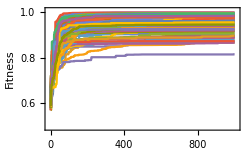

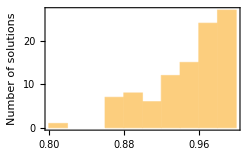

```mathematica
exp="../EvolutionData/D15_15";
maxfit=0.0;
maxind =-1;
allgens={};
allfit={};
bestgen={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgens=Append[allgens,y[[2]]];
allfit=Append[allfit,Last[y[[2]]]];
If[Last[y[[2]]]>maxfit,maxfit=Last[y[[2]]];maxind=i;];
If[Last[y[[2]]]>threshold,
file = StringJoin[exp,"/",ToString[i], "/best.gen.dat"];
x = Flatten[Import[file]];
bestgen=Append[bestgen,x];
];
];

maxind
ListLinePlot[Sqrt[allgens],PlotRange->{{-10,1010},{0.49,1.01}},Frame->True,FrameLabel->{"Generations","Fitness"},ImageSize->250]
(*Export["b.eps",%]*)
Histogram[Sqrt[allfit],Frame->True,FrameLabel->{"Fitness","Number of solutions"},ImageSize->250]
(*Export["b_hist.eps",%]*)
```

```mathematica
Sort[Table[{x-1,allfit[[x]]},{x,1,runnumber}],#1[[2]]>#2[[2]]&]
```

{{8,0.999116},{40,0.996214},{41,0.993225},{44,0.992133},{47,0.988893},{36,0.987976},{35,0.987679},{89,0.986497},{32,0.984766},{60,0.983063},{56,0.982089},{45,0.977026},{6,0.974869},{50,0.973284},{77,0.969796},{98,0.968448},{12,0.968284},{95,0.967134},{25,0.966143},{65,0.964348},{69,0.962232},{74,0.962089},{86,0.962033},{7,0.96171},{82,0.961422},{80,0.961316},{48,0.960894},{26,0.958128},{93,0.956264},{59,0.955971},{17,0.955456},{71,0.954435},{85,0.952321},{15,0.949777},{57,0.948681},{55,0.948451},{63,0.945221},{37,0.945126},{30,0.941239},{18,0.940601},{0,0.937144},{27,0.936352},{22,0.934288},{29,0.93085},{24,0.930647},{1,0.930619},{75,0.928946},{38,0.927751},{83,0.924461},{20,0.924208},{90,0.923663},{97,0.913583},{81,0.910908},{58,0.908725},{72,0.906484},{34,0.90383},{91,0.901542},{92,0.896932},{33,0.894074},{46,0.893973},{99,0.893439},{61,0.892643},{96,0.891397},{68,0.888765},{23,0.887213},{10,0.885592},{88,0.883365},{84,0.880909},{66,0.879954},{78,0.879248},{87,0.87588},{39,0.875421},{94,0.858035},{67,0.857153},{52,0.856775},{9,0.855085},{79,0.853468},{31,0.847331},{73,0.845617},{11,0.842956},{21,0.838846},{54,0.835584},{62,0.820679},{4,0.817009},{2,0.804168},{76,0.803908},{5,0.80066},{43,0.799385},{14,0.796299},{13,0.7921},{28,0.787885},{3,0.78211},{51,0.770268},{70,0.761592},{16,0.759718},{49,0.758258},{42,0.751805},{53,0.750357},{19,0.750087},{64,0.664061}}

```mathematica
(*DistributionChart[Transpose[bestgen],ChartStyle->"SouthwestColors",ChartElementFunction->"HistogramDensity",Frame->True,AspectRatio->1/10,FrameLabel->{"Parameters","Genotype value"},ImageSize->1200]
Export["Parameters.eps",%]*)
```

## Performance across circuit size (N=3,..,15)

```mathematica
runnumber=100;
```

```mathematica
exp="../cSrc/3";
allgens3={};
allfit3={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgens3=Append[allgens3,y[[2]]];
allfit3=Append[allfit3,Last[y[[2]]]];
];

exp="../cSrc/5";
allgens5={};
allfit5={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgens5=Append[allgens5,y[[2]]];
allfit5=Append[allfit5,Last[y[[2]]]];
];

exp="../cSrc/7";
allgens7={};
allfit7={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgens7=Append[allgens7,y[[2]]];
allfit7=Append[allfit7,Last[y[[2]]]];
];

exp="../cSrc/9";
allgens9={};
allfit9={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgens9=Append[allgens9,y[[2]]];
allfit9=Append[allfit9,Last[y[[2]]]];
];

exp="../cSrc/11";
allgens11={};
allfit11={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgens11=Append[allgens11,y[[2]]];
allfit11=Append[allfit11,Last[y[[2]]]];
];

exp="../cSrc/13";
allgens13={};
allfit13={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgens13=Append[allgens13,y[[2]]];
allfit13=Append[allfit13,Last[y[[2]]]];
];

exp="../cSrc/15";
allgens15={};
allfit15={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgens15=Append[allgens15,y[[2]]];
allfit15=Append[allfit15,Last[y[[2]]]];
];
```

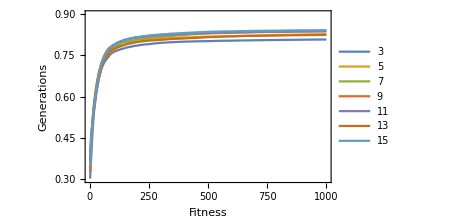

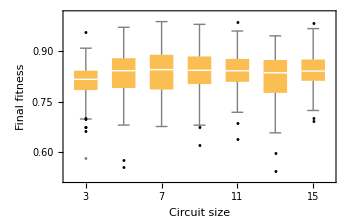

```mathematica
ListLinePlot[{Mean[allgens3],Mean[allgens5],Mean[allgens7],Mean[allgens9],Mean[allgens11],Mean[allgens13],Mean[allgens15]},PlotLegends->{"3","5","7","9","11","13","15"},PlotRange->{Automatic,{0.3,0.9}},Frame->True,ImageSize->350,FrameLabel->{"Fitness","Generations"}]
BoxWhiskerChart[{allfit3,allfit5,allfit7,allfit9,allfit11,allfit13,allfit15},"Outliers",ChartLabels->{"3","5","7","9","11","13","15"},Frame->True,FrameLabel->{"Circuit size","Final fitness"},ImageSize->350]
```

## Performance sensor size and typ4 (S=7 or 15 and )

```mathematica
runnumber=100;
```

```mathematica
exp="../EvolutionData/C7_5";
allgensC75={};
allfitC75={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgensC75=Append[allgensC75,y[[2]]];
allfitC75=Append[allfitC75,Last[y[[2]]]];
];

exp="../EvolutionData/C15_5";
allgensC155={};
allfitC155={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgensC155=Append[allgensC155,y[[2]]];
allfitC155=Append[allfitC155,Last[y[[2]]]];
];

exp="../EvolutionData/C15_10";
allgensC1510={};
allfitC1510={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgensC1510=Append[allgensC1510,y[[2]]];
allfitC1510=Append[allfitC1510,Last[y[[2]]]];
];

exp="../EvolutionData/C15_15";
allgensC1515={};
allfitC1515={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgensC1515=Append[allgensC1515,y[[2]]];
allfitC1515=Append[allfitC1515,Last[y[[2]]]];
];

exp="../EvolutionData/D7";
allgensD7={};
allfitD7={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgensD7=Append[allgensD7,y[[2]]];
allfitD7=Append[allfitD7,Last[y[[2]]]];
];

exp="../EvolutionData/D15_5";
allgensD155={};
allfitD155={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgensD155=Append[allgensD155,y[[2]]];
allfitD155=Append[allfitD155,Last[y[[2]]]];
];

exp="../EvolutionData/D15_10";
allgensD1510={};
allfitD1510={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgensD1510=Append[allgensD1510,y[[2]]];
allfitD1510=Append[allfitD1510,Last[y[[2]]]];
];

exp="../EvolutionData/D15_15";
allgensD1515={};
allfitD1515={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgensD1515=Append[allgensD1515,y[[2]]];
allfitD1515=Append[allfitD1515,Last[y[[2]]]];
];
```

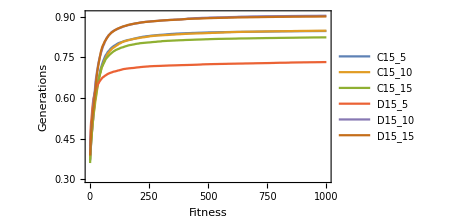

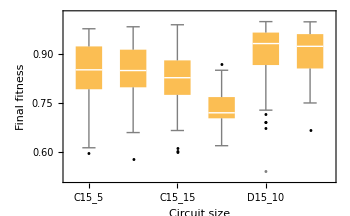

```mathematica
ListLinePlot[{Mean[allgensC155],Mean[allgensC1510],Mean[allgensC1515],Mean[allgensD155],Mean[allgensD1510],Mean[allgensD1515]},PlotLegends->{"C15_5","C15_10","C15_15","D15_5","D15_10","D15_15"},PlotRange->{Automatic,{0.3,0.91}},Frame->True,ImageSize->350,FrameLabel->{"Fitness","Generations"}]
BoxWhiskerChart[{allfitC155,allfitC1510,allfitC1515,allfitD155,allfitD1510,allfitD1515},"Outliers",ChartLabels->{"C15_5","C15_10","C15_15","D15_5","D15_10","D15_15"},Frame->True,FrameLabel->{"Circuit size","Final fitness"},ImageSize->350]
```